# Title

Author Name

Abstract

## Section

XXXX:

## Notes

Some statements come to us in the form.

Let n∈ℕ, or .

```mathematica
PositiveIntegers
```

(∀n≥M)(P(n)).

But we don't have to start with m.

For this we have the extended principle/principal of mathematical induction.

Let m be an integer. m∈ℤ.

If T is a subset of ℕ such that: T⊂ℕ

M∈T

∀ k ∈ℕ with k≥M, if k∈T then k+1∈T. if P(k) is true.

Then T contains all integers greater than or equal to M.

What is the link between this nice principle and P(n)?

principle

WolframAlphaQueryResults

We want to show the elements are related in what way.

We want to show that the elements in T make P(n) true!

How do we use this?

induction

WolframAlphaQueryResults

## Proof Example

How do we use this prove

(∀ n ∈ Integers, with n≥M)(P(n)).

Step 1: prove P(M) is true. (Anchor, basis, bottom ladder rung)

Step 2:Prove for k≥M, if P(k) is true then P(k+1) is true.

Step 3: Prove23 P(n) is true for n≥M.

Example:

Proposition: For all n∈ℕ, with n≥2, 3^1>1+2^n

```mathematica
FindInstance[3^n>1+2^n,{n},Integers]
```

{{n→198}}

Proof by induction:

Proposition: For All n ∈ N, 3^n>1+2^n:P(n).

From our above notation M=2.

First verify that P(n) holds for n=2.

```mathematica
And[Or[p,q],r]//BooleanConvert
```

(p&&r)||(q&&r)

```mathematica
Or[And[p,q],r]//BooleanConvert
```

(p&&q)||r

```mathematica
SameQ[p∨q∧r,p∧q∨r]
```

False

For the LHS we have 3^2=9

For the RHS we have 2^2+1=5

Since 9>5, P(2) is true.

Let P(k) be true for k≥2.

3^k>2^k+1

We want to show that 3^(k+1)>2^(k+1)+1 is true. This will show that P(k+1) is true.

```mathematica
3^(k+1)/3^k
```

3

```mathematica
(2^(k+1)+1)/(2^k+1)
```

(1+2^(1+k))/(1+2^k)

```mathematica
FullSimplify[(1+2^(1+k))/(1+2^k)]
```

2-1/(1+2^k)

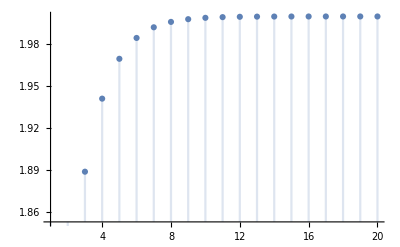

```mathematica
DiscretePlot[2-1/(1+2^k),{k,1,20}]
```

```mathematica
PowerExpand[3^(k+1)>2^(k+1)+1]
```

3^(1+k)>1+2^(1+k)

```mathematica
(3(3^k>2^k+1))//ExpandAll
```

3 (3^k>1+2^k)

```mathematica
MultiplySides[3^k>2^k+1,3]
```

3^(1+k)>3 (1+2^k)

3^(k+1)>3*2^k+3

3^(k+1)>3*2^k+3>2*2^k+1

3^(k+1)>3*2^k+3>2^(k+1)+1

Therefore P(k+1) follows from P(k). true

Hence the PMI, 3^n>2^n+1 for n≥2 .

prove by pmi 3^(k)>2^(k)+1 for k>=2 and k integer

WolframAlphaQueryResults

```mathematica
Reduce[∀_(k,{k∈Integers,k>=2})3^k>=2^k+1]
```

True

```mathematica
Reduce[∀_(k,{k∈Integers,k>=2})3^k>2^k+1]
```

True

∀ n ∈ ℕ, n is a prime number or n is a composite #.

n is either prime or the product of primes.

With our previous proposition, we used the truth of P(k) to show that P(k+1) is also true. That is P(k+1) follows from P(k).

Let k=13.

```mathematica
PrimeQ[13]
```

True

```mathematica
MangoldtLambda[13]
```

Log[13]

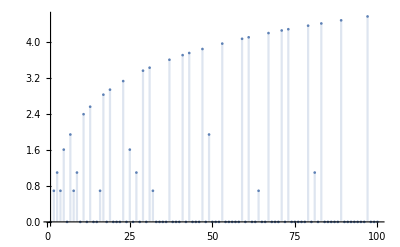

```mathematica
DiscretePlot[MangoldtLambda[n],{n,100}]
```

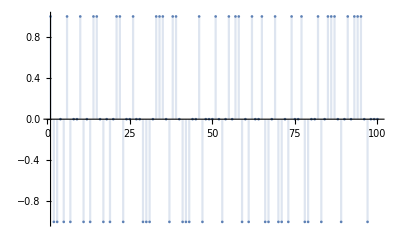

```mathematica
DiscretePlot[MoebiusMu[n],{n,100}]
```

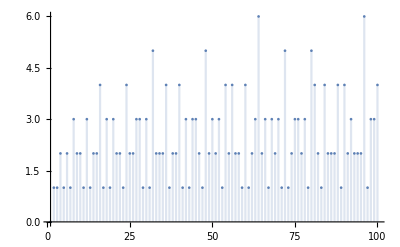

```mathematica
DiscretePlot[PrimeOmega[n],{n,100}]
```

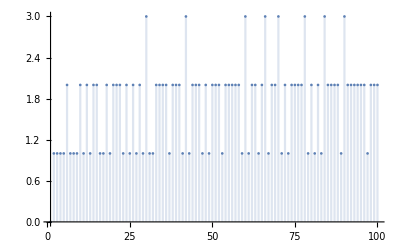

```mathematica
DiscretePlot[PrimeNu[n],{n,100}]
```

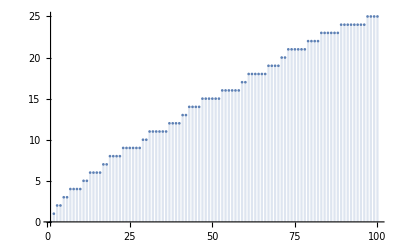

```mathematica
DiscretePlot[PrimePi[n],{n,100}]
```

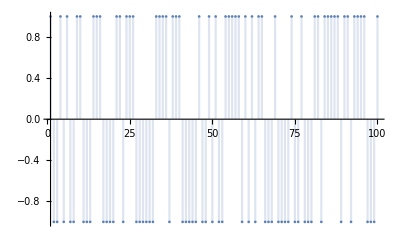

```mathematica
DiscretePlot[LiouvilleLambda[n],{n,100}]
```

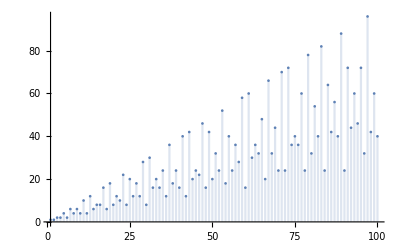

```mathematica
DiscretePlot[EulerPhi[n],{n,100}]
```

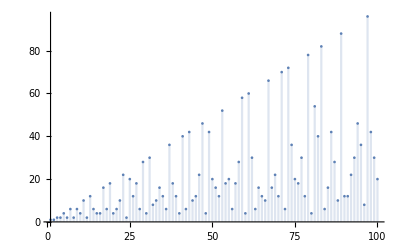

```mathematica
DiscretePlot[CarmichaelLambda[n],{n,100}]
```

Let k=13.

P(k)=P(13) is true since 13 is prime. We need to show that P(k+1)

```mathematica
Names["Prime*"]
```

{Prime,PrimeNu,PrimeOmega,PrimePi,PrimePowerQ,PrimeQ,Primes,PrimeZetaP}

## Fibonnaci

```mathematica
?Fibonacci
```

```mathematica
Asymptotic[Fibonacci[n],n->∞]
```

(1/2 (1+√5))^n/(√5)

```mathematica
Asymptotic[Fibonacci[n],n->∞,SeriesTermGoal->19]//TraditionalForm
```

ⅇ^(n (log(1+√5)-log(2)))/(√5)-(ⅇ^(n (-log(2)+log(4)-log(1+√5))) cos(π n))/(√5)

```mathematica
Table[Fibonacci[n],{n,20}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}

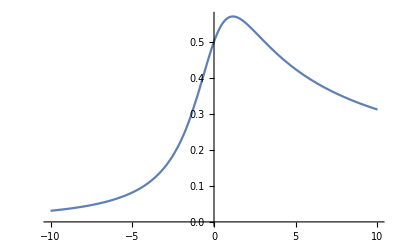

```mathematica
Plot[Fibonacci[1/2,x],{x,-10,10}]
```

```mathematica
ComplexPlot3D[Fibonacci[5/3,z],{z,-2-2I,2+2I},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Series[Fibonacci[1/2,x],{x,0,5}]//TraditionalForm
```

1/2+x/8-(3 x^2)/64-(5 x^3)/256+(35 x^4)/4096+(63 x^5)/16384+O(x^6)

```mathematica
Series[Fibonacci[1/2,x],{x,∞,5}]//FullSimplify//TraditionalForm
```

√(1/x)-3/2 (1/x)^(5/2)+O((1/x)^(9/2))

```mathematica
Series[Fibonacci[1/2,x],{x,-2I,3},Assumptions->x>1]//Normal//FullSimplify//TraditionalForm
```

((-1)^(3/4) x (-284+x (5 x+54 ⅈ))+2048/(√(x+2 ⅈ))+1416 -1^(1/4))/4096

```mathematica
Fibonacci[3.3]
```

2.24235

```mathematica
Fibonacci[0.4,CenteredInterval[1/2,1/200]]
```

```mathematica
Information[Fibonacci[0.4,CenteredInterval[1/2,1/200]],"Properties"]
```

{Bounds,Center,FullSpecification,Radius,Summary}

```mathematica
AssociationMap[Information[Fibonacci[0.4,CenteredInterval[1/2,1/200]],#]&,Information[Fibonacci[0.4,CenteredInterval[1/2,1/200]],"Properties"]]
```

<|Bounds→{109645006133/274877906944,110133538763/274877906944},Center→858509941/2147483648,FullSpecification→{{858509941,-31,977065260,-40},30},Radius→244266315/274877906944,Summary→{0.399774844,0.000888635677}|>

```mathematica
N[AssociationMap[Information[Fibonacci[0.4,CenteredInterval[1/2,1/200]],#]&,Information[Fibonacci[0.4,CenteredInterval[1/2,1/200]],"Properties"]]]
```

<|Bounds→{0.398886,0.400663},Center→0.399775,FullSpecification→{{8.5851×10^8,-31.,9.77065×10^8,-40.},30.},Radius→0.000888636,Summary→{0.399775,0.000888636}|>

```mathematica
Normal[Fibonacci[0.4,CenteredInterval[1/2,1/200]]]
```

0.4

Suppose a pair of rabbits one male and one female produces a pair of rabbits one male and one female each month. Suppose the babies become adults in two months?

```mathematica
TableForm[Table[{n,Fibonacci[n]},{n,100}]]
```

1 | 1
2 | 1
3 | 2
4 | 3
5 | 5
6 | 8
7 | 13
8 | 21
9 | 34
10 | 55
11 | 89
12 | 144
13 | 233
14 | 377
15 | 610
16 | 987
17 | 1597
18 | 2584
19 | 4181
20 | 6765
21 | 10946
22 | 17711
23 | 28657
24 | 46368
25 | 75025
26 | 121393
27 | 196418
28 | 317811
29 | 514229
30 | 832040
31 | 1346269
32 | 2178309
33 | 3524578
34 | 5702887
35 | 9227465
36 | 14930352
37 | 24157817
38 | 39088169
39 | 63245986
40 | 102334155
41 | 165580141
42 | 267914296
43 | 433494437
44 | 701408733
45 | 1134903170
46 | 1836311903
47 | 2971215073
48 | 4807526976
49 | 7778742049
50 | 12586269025
51 | 20365011074
52 | 32951280099
53 | 53316291173
54 | 86267571272
55 | 139583862445
56 | 225851433717
57 | 365435296162
58 | 591286729879
59 | 956722026041
60 | 1548008755920
61 | 2504730781961
62 | 4052739537881
63 | 6557470319842
64 | 10610209857723
65 | 17167680177565
66 | 27777890035288
67 | 44945570212853
68 | 72723460248141
69 | 117669030460994
70 | 190392490709135
71 | 308061521170129
72 | 498454011879264
73 | 806515533049393
74 | 1304969544928657
75 | 2111485077978050
76 | 3416454622906707
77 | 5527939700884757
78 | 8944394323791464
79 | 14472334024676221
80 | 23416728348467685
81 | 37889062373143906
82 | 61305790721611591
83 | 99194853094755497
84 | 160500643816367088
85 | 259695496911122585
86 | 420196140727489673
87 | 679891637638612258
88 | 1100087778366101931
89 | 1779979416004714189
90 | 2880067194370816120
91 | 4660046610375530309
92 | 7540113804746346429
93 | 12200160415121876738
94 | 19740274219868223167
95 | 31940434634990099905
96 | 51680708854858323072
97 | 83621143489848422977
98 | 135301852344706746049
99 | 218922995834555169026
100 | 354224848179261915075

months | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
adult pairs | 1 | 1 | 2 | 3 | 5 | 8 | 13 | 21 | 34
new born | 1 | 1 | 2 | □ | □ | □ | □ | □ | □
babies now adults | □ | 1 | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □

```mathematica
FindGeneratingFunction[LucasL[Range[10]],n]//Simplify//TraditionalForm
```

(-2 n-1)/(n^2+n-1)

```mathematica
FindGeneratingFunction[Fibonacci[Range[10]],n]//Simplify//TraditionalForm
```

-1/(n^2+n-1)

```mathematica
LucasSequence[m1_?IntegerQ,m2_?IntegerQ]:=RecurrenceTable[{a[n]==m1*a[n-1]-m2*a[n-2],a[1]==1,a[2]==1},a, 
  {n,10}]
```

```mathematica
RecurrenceTable[{a[n]==a[n-1]+a[n-2],a[1]==1,a[2]==1},a, 
  {n,10}]
```

{1,1,2,3,5,8,13,21,34,55}

```mathematica
LucasSequence[1,-1]
```

{1,1,2,3,5,8,13,21,34,55}

```mathematica
LucasSequence[2,-1]
```

{1,1,3,7,17,41,99,239,577,1393}

```mathematica
LucasSequence[1,-2]
```

{1,1,3,5,11,21,43,85,171,341}

```mathematica
LucasSequence[3,2]
```

{1,1,1,1,1,1,1,1,1,1}

This sequence is recursively defined. We have to have a starting point.

Then we need the formula to find the a_(n+1) knowing a_n. a_(n+1)=2 a_n-1

```mathematica
LucasUSequence[p_?IntegerQ,q_?IntegerQ]:=RecurrenceTable[{({{u[n,p,q]}, {u[n+1,p,q]}})==({{0, 1}, {-q, p}}).({{u[n-1,p,q]}, {u[n,p,q]}}), u[p,q]==0,u[1,p,q]==1},u,
  {n,10}]
```

```mathematica
LucasUSequence[1,1]
```

RecurrenceTable[{{{u[n,1,1]},{u[1+n,1,1]}}=={{u[n,1,1]},{-u[-1+n,1,1]+u[n,1,1]}}},u,{n,10}]